```mathematica
RSolve[{o[n]==Sum[o[i]*o[n-i],{i,0,n}],o[0]==1,o[1]==1},o[n],n]
```

RSolve[{o[n]==∑_(i=0)^n o[i] o[-i+n],o[0]==1,o[1]==1},o[n],n]

```mathematica
ClearAll[o];
o[0]=1;
o[1]=1;
o[n_]:=o[n]=Sum[o[i]*o[n-i],{i,1,n-1}];
```

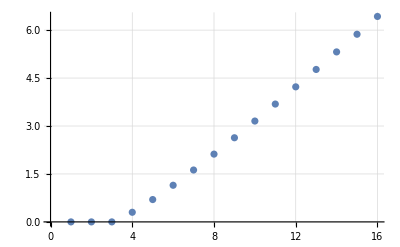

```mathematica
ListPlot[Log10[Table[o[n],{n,0,15}]],GridLines->Automatic]
```

```mathematica
With[{N=15,L=5},
With[{R=N+L-1},
Table[{Floor[L/2.+R/2.],
Floor[(L+R)/2.],
L+Floor[N/2.],
Floor[L +( N - 1)/2.]
}]]]
```

{12,12,12,12}

```mathematica
Module[{N=0},
With[{L=0},
{{"L","R","N",
"⌊(L+R)/2⌋",
"L+⌊N/2⌋",
"L+(N-1)/2 "}}~Join~
Table[With[{R=L+(N-1)},
{L,R,N,
Floor[(L+R)/2.],
L+Floor[N/2.],
L+N/2.+1/2.}],
{N,Range[2,15]}]]]//MatrixForm
```

(L | R | N | ⌊(L+R)/2⌋ | L+⌊N/2⌋ | L+(N-1)/2 
0 | 1 | 2 | 0 | 1 | 1.5
0 | 2 | 3 | 1 | 1 | 2.
0 | 3 | 4 | 1 | 2 | 2.5
0 | 4 | 5 | 2 | 2 | 3.
0 | 5 | 6 | 2 | 3 | 3.5
0 | 6 | 7 | 3 | 3 | 4.
0 | 7 | 8 | 3 | 4 | 4.5
0 | 8 | 9 | 4 | 4 | 5.
0 | 9 | 10 | 4 | 5 | 5.5
0 | 10 | 11 | 5 | 5 | 6.
0 | 11 | 12 | 5 | 6 | 6.5
0 | 12 | 13 | 6 | 6 | 7.
0 | 13 | 14 | 6 | 7 | 7.5
0 | 14 | 15 | 7 | 7 | 8.)